# Superconducting qubits Hub

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];*)
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
qubitsNum->6,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
StdPassiveNoise->True,
ZZPassiveNoise->True
};
```

```mathematica
dev=SuperconductingHub[];
```

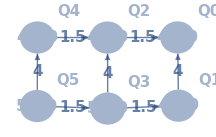

```mathematica
g=dev[Connectivity]
```

## Passive noise

### Simple test

```mathematica
noisycirc=
InsertCircuitNoise[{Sequence@@(Subscript[Init, #]&/@Range[0,5]),Subscript[Rx, 0][π],Subscript[Rx, 1][π],Subscript[Rx, 3][π/2],Subscript[ZX, 1,0],Subscript[ZZ, 4,5],Subscript[Rx, 0][π/4],Subscript[Rx, 1][π],Subscript[Rx, 2][π],Subscript[ZX, 2,0]},SuperconductingHub[]];
```

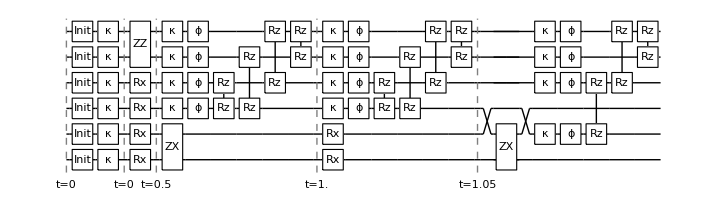

```mathematica
DrawCircuit[noisycirc]
```

### Initialisation

```mathematica
DestroyAllQuregs[];
ρinit=CreateDensityQureg[6];
ρ=CreateDensityQureg[6];
```

```mathematica
Values@OptionValue[SuperconductingHub,ExcitedInit]
```

{0.032,0.021,0.008,0.009,0.025,0.007}

```mathematica
noisycirc=InsertCircuitNoise[Subscript[Init, #]&/@Range[0,5],SuperconductingHub[],ReplaceAliases->True]
```

{{0,{Kraus_0[{{{0.98387,0.},{0.,0.}},{{0.,0.98387},{0.,0.}},{{0.,0.},{0.,0.178885}},{{0.,0.},{0.178885,0.}}}],Kraus_1[{{{0.989444,0.},{0.,0.}},{{0.,0.989444},{0.,0.}},{{0.,0.},{0.,0.144914}},{{0.,0.},{0.144914,0.}}}],Kraus_2[{{{0.995992,0.},{0.,0.}},{{0.,0.995992},{0.,0.}},{{0.,0.},{0.,0.0894427}},{{0.,0.},{0.0894427,0.}}}],Kraus_3[{{{0.99549,0.},{0.,0.}},{{0.,0.99549},{0.,0.}},{{0.,0.},{0.,0.0948683}},{{0.,0.},{0.0948683,0.}}}],Kraus_4[{{{0.987421,0.},{0.,0.}},{{0.,0.987421},{0.,0.}},{{0.,0.},{0.,0.158114}},{{0.,0.},{0.158114,0.}}}],Kraus_5[{{{0.996494,0.},{0.,0.}},{{0.,0.996494},{0.,0.}},{{0.,0.},{0.,0.083666}},{{0.,0.},{0.083666,0.}}}]},{}}}

```mathematica
(* initialise matrix as a random mix state, then apply the initialisation command *)
SetQuregMatrix[ρinit,RandomMixState[6]];
```

```mathematica
ApplyCircuit[ρinit,ExtractCircuit@noisycirc];
Diagonal@Re@GetQuregMatrix[ρinit]
```

{0.901981,0.0298175,0.0193479,0.0006396,0.00727404,0.000240464,0.000156031,5.15806×10^-6,0.00819155,0.000270795,0.000175713,5.80868×10^-6,0.0000660609,2.18383×10^-6,1.41704×10^-6,4.68442×10^-8,0.0231277,0.000764552,0.0004961,0.0000164,0.000186514,6.16575×10^-6,4.00081×10^-6,1.32258×10^-7,0.00021004,6.94346×10^-6,4.50545×10^-6,1.4894×10^-7,1.69387×10^-6,5.59957×10^-8,3.63343×10^-8,1.20113×10^-9,0.00635837,0.000210194,0.00013639,4.50876×10^-6,0.0000512772,1.69511×10^-6,1.09992×10^-6,3.6361×10^-8,0.0000577451,1.90893×10^-6,1.23866×10^-6,4.09474×10^-8,4.65686×10^-7,1.53946×10^-8,9.98918×10^-9,3.30221×10^-10,0.000163035,5.38959×10^-6,3.49718×10^-6,1.15609×10^-7,1.3148×10^-6,4.34645×10^-8,2.82031×10^-8,9.32333×10^-10,1.48064×10^-6,4.89469×10^-8,3.17605×10^-8,1.04993×10^-9,1.19407×10^-8,3.94733×10^-10,2.56133×10^-10,8.4672×10^-12}

```mathematica
(* Expected diagonals *)
Reverse@Diagonal[KroneckerProduct@@({{#,0},{0,1-#}}&/@(Values@OptionValue[SuperconductingHub,ExcitedInit]))]
```

{0.901981,0.00635837,0.0231277,0.000163035,0.00819155,0.0000577451,0.00021004,1.48064×10^-6,0.00727404,0.0000512772,0.000186514,1.3148×10^-6,0.0000660609,4.65686×10^-7,1.69387×10^-6,1.19407×10^-8,0.0193479,0.00013639,0.0004961,3.49718×10^-6,0.000175713,1.23866×10^-6,4.50545×10^-6,3.17605×10^-8,0.000156031,1.09992×10^-6,4.00081×10^-6,2.82031×10^-8,1.41704×10^-6,9.98918×10^-9,3.63343×10^-8,2.56133×10^-10,0.0298175,0.000210194,0.000764552,5.38959×10^-6,0.000270795,1.90893×10^-6,6.94346×10^-6,4.89469×10^-8,0.000240464,1.69511×10^-6,6.16575×10^-6,4.34645×10^-8,2.18383×10^-6,1.53946×10^-8,5.59957×10^-8,3.94733×10^-10,0.0006396,4.50876×10^-6,0.0000164,1.15609×10^-7,5.80868×10^-6,4.09474×10^-8,1.4894×10^-7,1.04993×10^-9,5.15806×10^-6,3.6361×10^-8,1.32258×10^-7,9.32333×10^-10,4.68442×10^-8,3.30221×10^-10,1.20113×10^-9,8.4672×10^-12}

### Thermal state

Assume ρinit is initialised to the initial state

```mathematica
noisycirc=InsertCircuitNoise[{Subscript[Wait, #][1]&/@Range[0,5]},SuperconductingHub[],ReplaceAliases->True]
```

{{0,{Kraus_0[{{{0.98387,0.},{0.,0.976092}},{{0.,0.123466},{0.,0.}},{{0.177471,0.},{0.,0.178885}},{{0.,0.},{0.0224483,0.}}}],Deph_0[0.00440526],Kraus_1[{{{0.989444,0.},{0.,0.984139}},{{0.,0.102325},{0.,0.}},{{0.144137,0.},{0.,0.144914}},{{0.,0.},{0.0149866,0.}}}],Deph_1[0.00334447],R[0.131923,Z_0 Z_1],Kraus_2[{{{0.995992,0.},{0.,0.991434}},{{0.,0.0951803},{0.,0.}},{{0.0890334,0.},{0.,0.0894427}},{{0.,0.},{0.00854745,0.}}}],Deph_2[0.00269541],R[-0.0277977,Z_0 Z_2],Kraus_3[{{{0.99549,0.},{0.,0.991171}},{{0.,0.0926285},{0.,0.}},{{0.0944568,0.},{0.,0.0948683}},{{0.,0.},{0.00882732,0.}}}],Deph_3[0.00309597],R[-0.0273321,Z_1 Z_3],R[0.133003,Z_2 Z_3],Kraus_4[{{{0.987421,0.},{0.,0.980187}},{{0.,0.119303},{0.,0.}},{{0.156956,0.},{0.,0.158114}},{{0.,0.},{0.0191038,0.}}}],Deph_4[0.00408161],R[-0.0276241,Z_2 Z_4],Kraus_5[{{{0.996494,0.},{0.,0.992516}},{{0.,0.0889512},{0.,0.}},{{0.083332,0.},{0.,0.083666}},{{0.,0.},{0.00746837,0.}}}],Deph_5[0.00249376],R[-0.0274045,Z_3 Z_5],R[0.132693,Z_4 Z_5]},{}}}

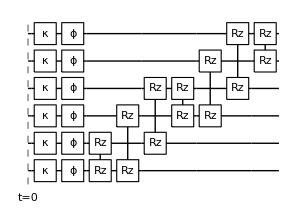

```mathematica
DrawCircuit[noisycirc]
```

```mathematica
δt=4;
dev=SuperconductingHub[];
SetQuregMatrix[ρ,RandomMixState[6]];
data=Table[
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Wait, #][δt]&/@Range[0,5],dev,ReplaceAliases->True]];
{t,CalcFidelityDensityMatrices[ρ,ρinit]}
,{t,δt,440,δt}];
```

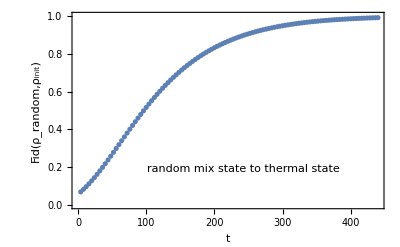

```mathematica
ListPlot[data,PlotRange->{Automatic,{0,1}},Frame->True,FrameLabel->{"t","Fid(ρ_random,ρ_init)"},FrameStyle->Directive[Black,Thick],ImageSize->400,BaseStyle->{17},Epilog->Inset["random mix state to thermal state",Scaled[{0.55,0.2}]]]
```

### T1 experiment

```mathematica
δt=4;
SetQuregMatrix[ρ,RandomMixState[6]];
dataT1=Table[
dev=SuperconductingHub[];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Init, #]&/@Range[0,5],dev,ReplaceAliases->True]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Rx, #][π]&/@Range[0,5],dev,ReplaceAliases->True]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Wait, #][t]&/@Range[0,5],dev,ReplaceAliases->True]];
{t,CalcProbOfOutcome[ρ,#,1]}&/@Range[0,5]
,{t,0,500,δt}];
```

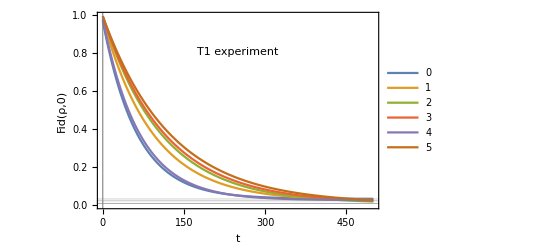

```mathematica
excp=Values@OptionValue[SuperconductingHub,ExcitedInit];
ListPlot[Transpose[dataT1],Frame->True,PlotLegends->Placed[Range[0,5],{0.9,0.5}],GridLines->{excp},Frame->True,FrameLabel->{"t","Fid(ρ,0)"},FrameStyle->Directive[Black,Thick],ImageSize->400,BaseStyle->{17},Epilog->Inset["T1 experiment",Scaled[{0.5,0.8}]],Joined->True]
```

### T2 experiment

```mathematica
δt=4;
SetQuregMatrix[ρ,RandomMixState[6]];
dataT2=Table[
dev=SuperconductingHub[];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Init, #]&/@Range[0,5],dev,ReplaceAliases->True]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Flatten[Subscript[Ry, #][π/2]&/@Range[0,5]],dev,ReplaceAliases->True]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Subscript[Wait, #][t]&/@Range[0,5],dev,ReplaceAliases->True]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Flatten[Subscript[Ry, #][-π/2]&/@Range[0,5]],dev,ReplaceAliases->True]];
{t,CalcProbOfOutcome[ρ,#,0]}&/@Range[0,5]
,{t,0,500,δt}];
```

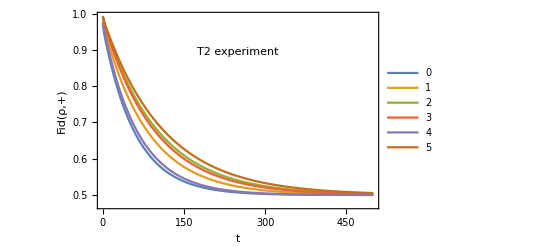

```mathematica
ListPlot[Transpose[dataT2],PlotLegends->Placed[Range[0,5],{0.9,0.55}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thick],ImageSize->400,FrameLabel->{"t","Fid(ρ,+)"},BaseStyle->{17},Epilog->Inset["T2 experiment",Scaled[{0.5,0.8}]],Joined->True]
```

## VQE on the virtual device: Solve H_2

```mathematica
Table[
fname=ToString@StringForm["H2/hamiltonian/H2_``.txt",NumberForm[dist,{2,2}]];
{ham,nterms,nq}=FormatHamiltonian[fname];
dev=SuperconductingHub[];
conf=DefaultConfig[dev,ham];
res=VQEonVQD[conf];
{runtime,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
AppendTo[H2onSQC,<|"description"->dist,"runtime"->runtime,"ansatz"->ansatz,"θvars"->θvars,"groundstate"->conf["grounstate"],"cycleres"->cycleres,"fev"->fev|>];
DumpSave["H2onSQC.mx",H2onSQC];
Print["dist ",dist," done with runtime ",runtime, " ϵ=",Last@Elist-conf["groundstate"]]
,{dist,0.05,1.5,0.05}];
```

Compilation with automatically generated ansatz at Tue 14 Feb 2023 16:55:24 with grad NGAN

@cycle1:Tue 14 Feb 2023 16:59:54, fev:1178, <E>: 7.981728413104717 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 51}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 17:03:04, fev:1899, <E>: 7.981728413104717 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 73}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 17:10:37, fev:2760, <E>: 7.981728413104717 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 112}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 17:37:56, fev:3983, <E>: 7.981728413104717 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 209}

dist 0.05 done with runtime 42.9191 min ϵ=0.0064874

Compilation with automatically generated ansatz at Tue 14 Feb 2023 17:38:19 with grad NGAN

@cycle1:Tue 14 Feb 2023 17:43:12, fev:1509, <E>: 2.717185782090246 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 1, 1, 19, 20}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 17:45:40, fev:2295, <E>: 2.717185782090246 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 1, 1, 19, 29}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 17:51:14, fev:3260, <E>: 2.717185782090246 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 1, 1, 19, 63}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 18:05:57, fev:4350, <E>: 2.717185782090246 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 1, 1, 19, 113}

dist 0.1 done with runtime 27.8127 min ϵ=0.00722501

Compilation with automatically generated ansatz at Tue 14 Feb 2023 18:06:08 with grad NGAN

@cycle1:Tue 14 Feb 2023 18:10:27, fev:1102, <E>: 0.9934710065359955 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 0, 1, 12, 33}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 18:11:51, fev:1736, <E>: 0.9934710065359955 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 0, 1, 12, 52}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 18:15:26, fev:2713, <E>: 0.9934710065359955 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 0, 1, 12, 76}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 18:25:03, fev:3902, <E>: 0.9934710065359955 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 0, 1, 12, 133}

dist 0.15 done with runtime 18.9211 min ϵ=0.00625161

Compilation with automatically generated ansatz at Tue 14 Feb 2023 18:25:04 with grad NGAN

@cycle1:Tue 14 Feb 2023 18:29:31, fev:1329, <E>: 0.16804267526147185 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 12, 37}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 18:31:34, fev:2016, <E>: 0.16804267526147185 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 12, 43}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 18:35:59, fev:3041, <E>: 0.16804267526147185 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 12, 62}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 18:45:37, fev:4165, <E>: 0.16804267526147185 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 12, 107}

dist 0.2 done with runtime 20.8972 min ϵ=0.0105605

Compilation with automatically generated ansatz at Tue 14 Feb 2023 18:45:57 with grad NGAN

@cycle1:Tue 14 Feb 2023 18:50:04, fev:1073, <E>: -0.3032291507023 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 51}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 18:51:58, fev:1590, <E>: -0.3032291507023 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 58}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 18:55:57, fev:2451, <E>: -0.3032291507023 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 68}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 19:03:51, fev:3577, <E>: -0.3032291507023 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 90}

dist 0.25 done with runtime 19.0481 min ϵ=0.00904075

Compilation with automatically generated ansatz at Tue 14 Feb 2023 19:05:00 with grad NGAN

@cycle1:Tue 14 Feb 2023 19:09:41, fev:1269, <E>: -0.5934339231382273 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 41}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 19:11:22, fev:1841, <E>: -0.5934339231382273 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 48}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 19:13:42, fev:2501, <E>: -0.5934339231382273 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 55}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 19:18:44, fev:3561, <E>: -0.5934339231382273 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 76}

dist 0.3 done with runtime 14.2914 min ϵ=0.00836979

Compilation with automatically generated ansatz at Tue 14 Feb 2023 19:19:18 with grad NGAN

@cycle1:Tue 14 Feb 2023 19:23:42, fev:1156, <E>: -0.7804499480528042 nansatz: 3 merged-smallθ-metric-bf-gmerged: {3, 6, 0, 13, 35}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 19:24:07, fev:1607, <E>: -0.7804499480528042 nansatz: 3 merged-smallθ-metric-bf-gmerged: {3, 6, 0, 13, 40}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 19:25:06, fev:2244, <E>: -0.7804499480528042 nansatz: 3 merged-smallθ-metric-bf-gmerged: {3, 6, 0, 13, 54}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 19:28:00, fev:3372, <E>: -0.7804499480528042 nansatz: 3 merged-smallθ-metric-bf-gmerged: {3, 6, 0, 13, 75}

dist 0.35 done with runtime 8.71815 min ϵ=0.00881944

Compilation with automatically generated ansatz at Tue 14 Feb 2023 19:28:01 with grad NGAN

@cycle1:Tue 14 Feb 2023 19:32:44, fev:1256, <E>: -0.9032537312923861 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 14, 33}

@cycle2:Tue 14 Feb 2023 19:34:05, fev:1961, <E>: -0.9040745461927115 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 19, 34}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 19:35:04, fev:2468, <E>: -0.9040745461927115 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 19, 36}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 19:37:02, fev:3162, <E>: -0.9040745461927115 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 19, 42}

I'm slowing down @cycle 5

@cycle5:Tue 14 Feb 2023 19:40:10, fev:4052, <E>: -0.9040745461927115 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 19, 53}

dist 0.4 done with runtime 12.321 min ϵ=0.0100752

Compilation with automatically generated ansatz at Tue 14 Feb 2023 19:40:20 with grad NGAN

@cycle1:Tue 14 Feb 2023 19:45:36, fev:1276, <E>: -0.9833213650080276 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 1, 0, 3, 52}

@cycle2:Tue 14 Feb 2023 19:46:13, fev:1794, <E>: -0.9875049908692038 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 3, 55}

@cycle3:Tue 14 Feb 2023 19:46:37, fev:2280, <E>: -0.9875089335408952 nansatz: 3 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 4, 60}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 19:46:58, fev:2725, <E>: -0.9875089335408952 nansatz: 3 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 4, 67}

I'm slowing down @cycle 5

@cycle5:Tue 14 Feb 2023 19:48:00, fev:3354, <E>: -0.9875089335408952 nansatz: 3 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 4, 73}

I'm slowing down @cycle 6

@cycle6:Tue 14 Feb 2023 19:49:41, fev:4294, <E>: -0.9875089335408952 nansatz: 3 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 4, 93}

dist 0.45 done with runtime 9.35281 min ϵ=0.0109067

Compilation with automatically generated ansatz at Tue 14 Feb 2023 19:49:41 with grad NGAN

@cycle1:Tue 14 Feb 2023 19:53:53, fev:1241, <E>: -1.042921471710426 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 16, 42}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 19:54:26, fev:1689, <E>: -1.042921471710426 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 16, 44}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 19:55:16, fev:2232, <E>: -1.042921471710426 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 16, 45}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 19:57:07, fev:3110, <E>: -1.042921471710426 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 16, 49}

dist 0.5 done with runtime 7.4638 min ϵ=0.0122383

Compilation with automatically generated ansatz at Tue 14 Feb 2023 19:57:09 with grad NGAN

@cycle1:Tue 14 Feb 2023 20:02:19, fev:1454, <E>: -1.0790116662969538 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 0, 0, 26, 45}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 20:02:47, fev:1899, <E>: -1.0790116662969538 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 0, 0, 26, 49}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 20:03:31, fev:2487, <E>: -1.0790116662969538 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 0, 0, 26, 56}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 20:04:58, fev:3340, <E>: -1.0790116662969538 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 0, 0, 26, 66}

dist 0.55 done with runtime 7.82876 min ϵ=0.0136182

Compilation with automatically generated ansatz at Tue 14 Feb 2023 20:04:59 with grad NGAN

@cycle1:Tue 14 Feb 2023 20:10:46, fev:1396, <E>: -1.0843398682634149 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 0, 3, 11, 43}

@cycle2:Tue 14 Feb 2023 20:11:20, fev:1888, <E>: -1.1010422388175092 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 17, 45}

@cycle3:Tue 14 Feb 2023 20:11:37, fev:2308, <E>: -1.1010452996041282 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 17, 48}

@cycle4:Tue 14 Feb 2023 20:11:56, fev:2800, <E>: -1.101048564207714 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 18, 50}

@cycle5:Tue 14 Feb 2023 20:12:12, fev:3232, <E>: -1.1011119724735197 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 18, 50}

Join::heads: Heads List and Missing at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

@cycle6:Tue 14 Feb 2023 20:12:32, fev:3703, <E>: -1.1011119725021858 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 20, 52}

I'm slowing down @cycle 7

@cycle7:Tue 14 Feb 2023 20:12:53, fev:4169, <E>: -1.1011119725021858 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 20, 54}

I'm slowing down @cycle 8

@cycle8:Tue 14 Feb 2023 20:13:37, fev:4901, <E>: -1.1011119725021858 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 20, 56}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 20:14:51, fev:5701, <E>: -1.1011119725021858 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 4, 3, 20, 63}

dist 0.6 done with runtime 9.88599 min ϵ=0.015174

Compilation with automatically generated ansatz at Tue 14 Feb 2023 20:14:52 with grad NGAN

@cycle1:Tue 14 Feb 2023 20:19:14, fev:1075, <E>: -1.1081208486062195 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 3, 56}

@cycle2:Tue 14 Feb 2023 20:19:34, fev:1539, <E>: -1.1123647689045728 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 4, 58}

@cycle3:Tue 14 Feb 2023 20:19:54, fev:2012, <E>: -1.1129165465119155 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 6, 60}

@cycle4:Tue 14 Feb 2023 20:20:07, fev:2492, <E>: -1.112919557659702 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 7, 62}

@cycle5:Tue 14 Feb 2023 20:20:25, fev:2904, <E>: -1.112990685229968 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 8, 65}

@cycle6:Tue 14 Feb 2023 20:20:41, fev:3368, <E>: -1.1129937095236095 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 8, 68}

@cycle7:Tue 14 Feb 2023 20:20:55, fev:3816, <E>: -1.1129965452509643 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 9, 72}

@cycle8:Tue 14 Feb 2023 20:21:18, fev:4272, <E>: -1.1129965454040431 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 9, 77}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 20:21:34, fev:4716, <E>: -1.1129965454040431 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 9, 80}

I'm slowing down @cycle 10

@cycle10:Tue 14 Feb 2023 20:22:05, fev:5276, <E>: -1.1129965454040431 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 9, 85}

I'm slowing down @cycle 11

@cycle11:Tue 14 Feb 2023 20:23:08, fev:6013, <E>: -1.1129965454040431 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 9, 94}

dist 0.65 done with runtime 8.27971 min ϵ=0.0169082

Compilation with automatically generated ansatz at Tue 14 Feb 2023 20:23:09 with grad NGAN

@cycle1:Tue 14 Feb 2023 20:28:02, fev:1324, <E>: -1.1169334346878625 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 1, 3, 11, 31}

@cycle2:Tue 14 Feb 2023 20:28:30, fev:1813, <E>: -1.1169360413584362 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 1, 3, 11, 33}

@cycle3:Tue 14 Feb 2023 20:28:59, fev:2305, <E>: -1.1169360418397076 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 1, 3, 13, 33}

@cycle4:Tue 14 Feb 2023 20:29:29, fev:2799, <E>: -1.1172152949037757 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 5, 3, 14, 35}

@cycle5:Tue 14 Feb 2023 20:29:44, fev:3272, <E>: -1.117294854473059 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 5, 3, 16, 36}

@cycle6:Tue 14 Feb 2023 20:30:10, fev:3784, <E>: -1.11729500116517 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 5, 3, 17, 37}

@cycle7:Tue 14 Feb 2023 20:30:24, fev:4252, <E>: -1.1173228871079124 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 5, 3, 18, 38}

I'm slowing down @cycle 8

@cycle8:Tue 14 Feb 2023 20:30:41, fev:4696, <E>: -1.1173228871079124 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 5, 3, 18, 39}

@cycle9:Tue 14 Feb 2023 20:31:17, fev:5302, <E>: -1.117349034801301 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 5, 3, 18, 40}

I'm slowing down @cycle 10

@cycle10:Tue 14 Feb 2023 20:32:00, fev:5923, <E>: -1.117349034801301 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 5, 3, 18, 40}

I'm slowing down @cycle 11

@cycle11:Tue 14 Feb 2023 20:33:13, fev:6689, <E>: -1.117349034801301 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 5, 3, 18, 41}

I'm slowing down @cycle 12

@cycle12:Tue 14 Feb 2023 20:34:14, fev:7461, <E>: -1.117349034801301 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 5, 3, 18, 42}

dist 0.7 done with runtime 11.1188 min ϵ=0.0188404

Compilation with automatically generated ansatz at Tue 14 Feb 2023 20:34:16 with grad NGAN

@cycle1:Tue 14 Feb 2023 20:38:58, fev:1227, <E>: -1.115824993631499 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 14, 32}

@cycle2:Tue 14 Feb 2023 20:39:41, fev:1846, <E>: -1.1161246651646588 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 16, 33}

@cycle3:Tue 14 Feb 2023 20:40:22, fev:2390, <E>: -1.1161246651939498 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 18, 33}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 20:40:50, fev:2834, <E>: -1.1161246651939498 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 18, 34}

I'm slowing down @cycle 5

@cycle5:Tue 14 Feb 2023 20:41:33, fev:3377, <E>: -1.1161246651939498 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 18, 34}

I'm slowing down @cycle 6

@cycle6:Tue 14 Feb 2023 20:42:44, fev:4027, <E>: -1.1161246651939498 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 18, 39}

dist 0.75 done with runtime 8.57487 min ϵ=0.0209924

Compilation with automatically generated ansatz at Tue 14 Feb 2023 20:42:51 with grad NGAN

@cycle1:Tue 14 Feb 2023 20:48:21, fev:1339, <E>: -1.109220444546701 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 6, 52}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 20:49:01, fev:1783, <E>: -1.109220444546701 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 6, 55}

@cycle3:Tue 14 Feb 2023 20:50:17, fev:2494, <E>: -1.1106741083501435 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 10, 58}

@cycle4:Tue 14 Feb 2023 20:51:30, fev:3179, <E>: -1.1106741087880674 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 11, 60}

@cycle5:Tue 14 Feb 2023 20:52:27, fev:3781, <E>: -1.110700523051437 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 11, 64}

@cycle6:Tue 14 Feb 2023 20:53:44, fev:4504, <E>: -1.110724103998237 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 12, 68}

@cycle7:Tue 14 Feb 2023 20:54:42, fev:5126, <E>: -1.11075015972984 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 12, 70}

@cycle8:Tue 14 Feb 2023 20:55:49, fev:5787, <E>: -1.1107749723526974 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 12, 72}

@cycle9:Tue 14 Feb 2023 20:56:56, fev:6429, <E>: -1.110782886157582 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 12, 75}

@cycle10:Tue 14 Feb 2023 20:58:00, fev:7147, <E>: -1.11078513208635 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 13, 75}

@cycle11:Tue 14 Feb 2023 20:59:12, fev:7849, <E>: -1.1107857026656998 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 14, 77}

@cycle12:Tue 14 Feb 2023 21:00:12, fev:8440, <E>: -1.1107864051308602 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 14, 79}

@cycle13:Tue 14 Feb 2023 21:01:31, fev:9181, <E>: -1.1107864053178695 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 16, 81}

I'm slowing down @cycle 14

@cycle14:Tue 14 Feb 2023 21:02:22, fev:9677, <E>: -1.1107864053178695 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 16, 81}

I'm slowing down @cycle 15

@cycle15:Tue 14 Feb 2023 21:03:53, fev:10379, <E>: -1.1107864053178695 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 16, 88}

I'm slowing down @cycle 16

@cycle16:Tue 14 Feb 2023 21:05:38, fev:11181, <E>: -1.1107864053178695 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 16, 91}

dist 0.8 done with runtime 22.9959 min ϵ=0.0233613

Compilation with automatically generated ansatz at Tue 14 Feb 2023 21:05:51 with grad NGAN

@cycle1:Tue 14 Feb 2023 21:10:31, fev:1259, <E>: -1.1024883500302403 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 18, 54}

@cycle2:Tue 14 Feb 2023 21:10:54, fev:1803, <E>: -1.1024883501412917 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 20, 55}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 21:11:11, fev:2247, <E>: -1.1024883501412917 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 20, 56}

@cycle4:Tue 14 Feb 2023 21:11:47, fev:2895, <E>: -1.1025105539245261 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 21, 56}

@cycle5:Tue 14 Feb 2023 21:12:17, fev:3535, <E>: -1.102510553924579 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 23, 56}

I'm slowing down @cycle 6

@cycle6:Tue 14 Feb 2023 21:12:53, fev:4091, <E>: -1.102510553924579 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 23, 58}

I'm slowing down @cycle 7

@cycle7:Tue 14 Feb 2023 21:13:55, fev:4829, <E>: -1.102510553924579 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 23, 60}

I'm slowing down @cycle 8

@cycle8:Tue 14 Feb 2023 21:15:11, fev:5687, <E>: -1.102510553924579 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 0, 2, 23, 65}

dist 0.85 done with runtime 9.38697 min ϵ=0.0258513

Compilation with automatically generated ansatz at Tue 14 Feb 2023 21:15:14 with grad NGAN

@cycle1:Tue 14 Feb 2023 21:21:11, fev:1550, <E>: -1.091875431011387 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 46}

@cycle2:Tue 14 Feb 2023 21:21:54, fev:2102, <E>: -1.0918946917725425 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 46}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 21:22:13, fev:2502, <E>: -1.0918946917725425 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 46}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 21:23:04, fev:3202, <E>: -1.0918946917725425 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 46}

I'm slowing down @cycle 5

@cycle5:Tue 14 Feb 2023 21:24:03, fev:3839, <E>: -1.0918946917725425 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 46}

dist 0.9 done with runtime 8.95812 min ϵ=0.0286656

Compilation with automatically generated ansatz at Tue 14 Feb 2023 21:24:11 with grad NGAN

@cycle1:Tue 14 Feb 2023 21:28:24, fev:1119, <E>: -1.0796332016306291 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 8, 40}

@cycle2:Tue 14 Feb 2023 21:28:33, fev:1539, <E>: -1.079635004919943 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 8, 40}

@cycle3:Tue 14 Feb 2023 21:28:48, fev:2003, <E>: -1.079635005128174 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 8, 43}

@cycle4:Tue 14 Feb 2023 21:29:08, fev:2471, <E>: -1.0796369281127025 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 8, 46}

I'm slowing down @cycle 5

@cycle5:Tue 14 Feb 2023 21:29:20, fev:2871, <E>: -1.0796369281127025 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 8, 51}

@cycle6:Tue 14 Feb 2023 21:29:45, fev:3451, <E>: -1.0796369282021259 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 9, 56}

I'm slowing down @cycle 7

@cycle7:Tue 14 Feb 2023 21:30:13, fev:3990, <E>: -1.0796369282021259 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 9, 59}

@cycle8:Tue 14 Feb 2023 21:30:46, fev:4671, <E>: -1.0796369282028802 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 10, 64}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 21:31:27, fev:5360, <E>: -1.0796369282028802 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 10, 69}

I'm slowing down @cycle 10

@cycle10:Tue 14 Feb 2023 21:32:14, fev:6093, <E>: -1.0796369282028802 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 10, 78}

I'm slowing down @cycle 11

@cycle11:Tue 14 Feb 2023 21:33:24, fev:6994, <E>: -1.0796369282028802 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 10, 83}

dist 0.95 done with runtime 9.22539 min ϵ=0.0317025

Compilation with automatically generated ansatz at Tue 14 Feb 2023 21:33:25 with grad NGAN

@cycle1:Tue 14 Feb 2023 21:37:53, fev:1191, <E>: -1.0660873251618326 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 23, 34}

@cycle2:Tue 14 Feb 2023 21:38:13, fev:1677, <E>: -1.0660907858567603 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 23, 35}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 21:38:31, fev:2121, <E>: -1.0660907858567603 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 23, 37}

@cycle4:Tue 14 Feb 2023 21:39:08, fev:2752, <E>: -1.0660907859280857 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 24, 40}

@cycle5:Tue 14 Feb 2023 21:39:47, fev:3385, <E>: -1.0660907859297393 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 26, 41}

@cycle6:Tue 14 Feb 2023 21:40:21, fev:4041, <E>: -1.0661086492920895 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 27, 42}

@cycle7:Tue 14 Feb 2023 21:41:03, fev:4723, <E>: -1.0661086493156213 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 28, 45}

@cycle8:Tue 14 Feb 2023 21:41:36, fev:5360, <E>: -1.066108649317936 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 30, 46}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 21:42:11, fev:5930, <E>: -1.066108649317936 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 30, 49}

I'm slowing down @cycle 10

@cycle10:Tue 14 Feb 2023 21:42:46, fev:6566, <E>: -1.066108649317936 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 30, 51}

I'm slowing down @cycle 11

@cycle11:Tue 14 Feb 2023 21:43:46, fev:7324, <E>: -1.066108649317936 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 30, 56}

dist 1. done with runtime 10.4046 min ϵ=0.0350417

Compilation with automatically generated ansatz at Tue 14 Feb 2023 21:43:49 with grad NGAN

@cycle1:Tue 14 Feb 2023 21:47:51, fev:1118, <E>: -1.036121352451952 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 18, 22}

@cycle2:Tue 14 Feb 2023 21:48:08, fev:1610, <E>: -1.036475997034238 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 22, 23}

@cycle3:Tue 14 Feb 2023 21:48:26, fev:2082, <E>: -1.036491414235798 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 22, 24}

@cycle4:Tue 14 Feb 2023 21:48:45, fev:2569, <E>: -1.036508450734189 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 22, 24}

@cycle5:Tue 14 Feb 2023 21:49:12, fev:3079, <E>: -1.0365229019339353 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 22, 26}

@cycle6:Tue 14 Feb 2023 21:49:36, fev:3571, <E>: -1.0365243507038995 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 22, 28}

@cycle7:Tue 14 Feb 2023 21:49:59, fev:4111, <E>: -1.0365243507190756 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 23, 29}

I'm slowing down @cycle 8

@cycle8:Tue 14 Feb 2023 21:50:19, fev:4467, <E>: -1.0365243507190756 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 23, 29}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 21:50:50, fev:5011, <E>: -1.0365243507190756 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 23, 31}

I'm slowing down @cycle 10

@cycle10:Tue 14 Feb 2023 21:51:45, fev:5669, <E>: -1.0365243507190756 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 23, 34}

dist 1.05 done with runtime 8.00836 min ϵ=0.0426686

Compilation with automatically generated ansatz at Tue 14 Feb 2023 21:51:50 with grad NGAN

@cycle1:Tue 14 Feb 2023 21:56:49, fev:1390, <E>: -1.0365388750234514 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 24, 49}

I'm slowing down @cycle 2

@cycle2:Tue 14 Feb 2023 21:57:09, fev:1790, <E>: -1.0365388750234514 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 24, 50}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 21:57:37, fev:2338, <E>: -1.0365388750234514 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 24, 51}

@cycle4:Tue 14 Feb 2023 21:58:29, fev:3091, <E>: -1.036538875029168 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 25, 57}

I'm slowing down @cycle 5

@cycle5:Tue 14 Feb 2023 21:59:07, fev:3728, <E>: -1.036538875029168 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 25, 60}

I'm slowing down @cycle 6

@cycle6:Tue 14 Feb 2023 21:59:56, fev:4474, <E>: -1.036538875029168 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 25, 65}

I'm slowing down @cycle 7

@cycle7:Tue 14 Feb 2023 22:00:53, fev:5323, <E>: -1.036538875029168 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 25, 69}

dist 1.1 done with runtime 9.07266 min ϵ=0.0426541

Compilation with automatically generated ansatz at Tue 14 Feb 2023 22:00:54 with grad NGAN

@cycle1:Tue 14 Feb 2023 22:06:08, fev:1296, <E>: -1.0009105095156745 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 0, 30}

@cycle2:Tue 14 Feb 2023 22:07:34, fev:2004, <E>: -1.0050335456173483 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 27, 30}

@cycle3:Tue 14 Feb 2023 22:07:53, fev:2504, <E>: -1.0050335456294586 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 27, 30}

@cycle4:Tue 14 Feb 2023 22:08:10, fev:2980, <E>: -1.0050460851171987 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 27, 32}

I'm slowing down @cycle 5

@cycle5:Tue 14 Feb 2023 22:08:23, fev:3424, <E>: -1.0050460851171987 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 27, 33}

I'm slowing down @cycle 6

@cycle6:Tue 14 Feb 2023 22:08:45, fev:3969, <E>: -1.0050460851171987 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 27, 33}

@cycle7:Tue 14 Feb 2023 22:09:27, fev:4642, <E>: -1.0050941069777137 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 27, 34}

I'm slowing down @cycle 8

@cycle8:Tue 14 Feb 2023 22:10:03, fev:5321, <E>: -1.0050941069777137 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 27, 34}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 22:10:41, fev:6056, <E>: -1.0050941069777137 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 27, 34}

I'm slowing down @cycle 10

@cycle10:Tue 14 Feb 2023 22:11:30, fev:6931, <E>: -1.0050941069777137 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 27, 34}

dist 1.15 done with runtime 10.6155 min ϵ=0.0516466

Compilation with automatically generated ansatz at Tue 14 Feb 2023 22:11:31 with grad NGAN

@cycle1:Tue 14 Feb 2023 22:16:17, fev:1104, <E>: -1.005104097486936 nansatz: 2 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 7, 43}

@cycle2:Tue 14 Feb 2023 22:16:30, fev:1568, <E>: -1.0051054439402498 nansatz: 3 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 7, 45}

@cycle3:Tue 14 Feb 2023 22:16:41, fev:2032, <E>: -1.0051054439836804 nansatz: 3 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 7, 47}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 22:16:56, fev:2432, <E>: -1.0051054439836804 nansatz: 3 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 7, 48}

@cycle5:Tue 14 Feb 2023 22:17:18, fev:3001, <E>: -1.0051067065461239 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 7, 51}

I'm slowing down @cycle 6

@cycle6:Tue 14 Feb 2023 22:17:47, fev:3557, <E>: -1.0051067065461239 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 7, 53}

@cycle7:Tue 14 Feb 2023 22:18:24, fev:4243, <E>: -1.0051067065665513 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 9, 58}

I'm slowing down @cycle 8

@cycle8:Tue 14 Feb 2023 22:19:06, fev:4936, <E>: -1.0051067065665513 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 9, 63}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 22:19:47, fev:5752, <E>: -1.0051067065665513 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 9, 67}

I'm slowing down @cycle 10

@cycle10:Tue 14 Feb 2023 22:20:17, fev:6611, <E>: -1.0051067065665513 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 4, 0, 9, 71}

dist 1.2 done with runtime 8.78177 min ϵ=0.051634

Compilation with automatically generated ansatz at Tue 14 Feb 2023 22:20:18 with grad NGAN

@cycle1:Tue 14 Feb 2023 22:25:01, fev:1371, <E>: -0.9727155883448958 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 16, 39}

@cycle2:Tue 14 Feb 2023 22:25:39, fev:1907, <E>: -0.972715588523014 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 17, 39}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 22:26:03, fev:2307, <E>: -0.972715588523014 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 17, 39}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 22:26:31, fev:2791, <E>: -0.972715588523014 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 17, 39}

I'm slowing down @cycle 5

@cycle5:Tue 14 Feb 2023 22:27:17, fev:3419, <E>: -0.972715588523014 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 17, 39}

dist 1.25 done with runtime 7.07011 min ϵ=0.0624707

Compilation with automatically generated ansatz at Tue 14 Feb 2023 22:27:22 with grad NGAN

@cycle1:Tue 14 Feb 2023 22:31:51, fev:1217, <E>: -0.9677585590414707 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 7, 46}

@cycle2:Tue 14 Feb 2023 22:33:09, fev:1869, <E>: -0.9677585591791513 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 9, 46}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 22:33:49, fev:2225, <E>: -0.9677585591791513 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 9, 47}

I'm slowing down @cycle 4

@cycle4:Tue 14 Feb 2023 22:34:47, fev:2757, <E>: -0.9677585591791513 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 9, 47}

I'm slowing down @cycle 5

@cycle5:Tue 14 Feb 2023 22:35:55, fev:3391, <E>: -0.9677585591791513 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 9, 47}

dist 1.3 done with runtime 8.80174 min ϵ=0.0674277

Compilation with automatically generated ansatz at Tue 14 Feb 2023 22:36:10 with grad NGAN

@cycle1:Tue 14 Feb 2023 22:41:02, fev:1216, <E>: -0.9412408388650803 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 3, 1, 16, 38}

@cycle2:Tue 14 Feb 2023 22:41:32, fev:1798, <E>: -0.9414495334532049 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 5, 1, 21, 38}

@cycle3:Tue 14 Feb 2023 22:41:45, fev:2246, <E>: -0.9414509997232575 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 5, 1, 21, 38}

@cycle4:Tue 14 Feb 2023 22:41:56, fev:2710, <E>: -0.9414610656356093 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 5, 1, 21, 39}

@cycle5:Tue 14 Feb 2023 22:42:13, fev:3202, <E>: -0.9414610656694393 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 5, 1, 22, 40}

@cycle6:Tue 14 Feb 2023 22:42:32, fev:3682, <E>: -0.9414711752663352 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 5, 1, 22, 41}

@cycle7:Tue 14 Feb 2023 22:42:47, fev:4193, <E>: -0.9414711754758633 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 6, 1, 22, 41}

I'm slowing down @cycle 8

@cycle8:Tue 14 Feb 2023 22:43:21, fev:4780, <E>: -0.9414711754758633 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 6, 1, 22, 43}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 22:43:49, fev:5408, <E>: -0.9414711754758633 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 6, 1, 22, 44}

I'm slowing down @cycle 10

@cycle10:Tue 14 Feb 2023 22:44:28, fev:6102, <E>: -0.9414711754758633 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 6, 1, 22, 46}

dist 1.35 done with runtime 8.30824 min ϵ=0.0739971

Compilation with automatically generated ansatz at Tue 14 Feb 2023 22:44:29 with grad NGAN

@cycle1:Tue 14 Feb 2023 22:48:57, fev:1178, <E>: -0.9408988630320679 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 8, 47}

@cycle2:Tue 14 Feb 2023 22:50:22, fev:1859, <E>: -0.9408988630459293 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 9, 48}

@cycle3:Tue 14 Feb 2023 22:51:38, fev:2528, <E>: -0.9394795576610928 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 14, 48}

@cycle4:Tue 14 Feb 2023 22:52:18, fev:3099, <E>: -0.9394795577613206 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 14, 49}

@cycle5:Tue 14 Feb 2023 22:52:51, fev:3633, <E>: -0.9392895141361272 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 18, 49}

@cycle6:Tue 14 Feb 2023 22:53:13, fev:4142, <E>: -0.9414796418223945 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 18, 49}

@cycle7:Tue 14 Feb 2023 22:53:31, fev:4620, <E>: -0.9414796418333207 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 19, 51}

I'm slowing down @cycle 8

@cycle8:Tue 14 Feb 2023 22:53:50, fev:5108, <E>: -0.9414796418333207 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 19, 51}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 22:54:10, fev:5664, <E>: -0.9414796418333207 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 19, 53}

I'm slowing down @cycle 10

@cycle10:Tue 14 Feb 2023 22:54:35, fev:6318, <E>: -0.9414796418333207 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 19, 54}

dist 1.4 done with runtime 10.1401 min ϵ=0.0739886

Compilation with automatically generated ansatz at Tue 14 Feb 2023 22:54:37 with grad NGAN

@cycle1:Tue 14 Feb 2023 22:59:32, fev:1284, <E>: -0.9086573994547138 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 0, 1, 20, 31}

@cycle2:Tue 14 Feb 2023 23:00:15, fev:1888, <E>: -0.9087312886155056 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 0, 1, 21, 34}

@cycle3:Tue 14 Feb 2023 23:01:03, fev:2505, <E>: -0.9087709128792827 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 0, 1, 21, 34}

@cycle4:Tue 14 Feb 2023 23:02:01, fev:3196, <E>: -0.9087709128847283 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 0, 1, 22, 36}

@cycle5:Tue 14 Feb 2023 23:02:49, fev:3783, <E>: -0.9087870829326691 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 0, 1, 22, 38}

@cycle6:Tue 14 Feb 2023 23:03:35, fev:4404, <E>: -0.9088269268086341 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 0, 1, 22, 39}

I'm slowing down @cycle 7

@cycle7:Tue 14 Feb 2023 23:04:07, fev:4804, <E>: -0.9088269268086341 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 0, 1, 22, 40}

I'm slowing down @cycle 8

@cycle8:Tue 14 Feb 2023 23:04:45, fev:5336, <E>: -0.9088269268086341 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 0, 1, 22, 40}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 23:05:43, fev:5990, <E>: -0.9088269268086341 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 0, 1, 22, 41}

dist 1.45 done with runtime 11.2734 min ϵ=0.0893224

Compilation with automatically generated ansatz at Tue 14 Feb 2023 23:05:54 with grad NGAN

@cycle1:Tue 14 Feb 2023 23:10:20, fev:1260, <E>: -0.9081533930078467 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 19, 44}

@cycle2:Tue 14 Feb 2023 23:10:57, fev:1899, <E>: -0.9081533932449817 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 20, 44}

I'm slowing down @cycle 3

@cycle3:Tue 14 Feb 2023 23:11:17, fev:2299, <E>: -0.9081533932449817 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 20, 44}

@cycle4:Tue 14 Feb 2023 23:12:00, fev:2995, <E>: -0.9108247636198068 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 25, 44}

@cycle5:Tue 14 Feb 2023 23:12:34, fev:3604, <E>: -0.9108647890414151 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 25, 44}

I'm slowing down @cycle 6

@cycle6:Tue 14 Feb 2023 23:12:57, fev:4136, <E>: -0.9108647890414151 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 25, 45}

@cycle7:Tue 14 Feb 2023 23:13:40, fev:4896, <E>: -0.9108647890595537 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 27, 46}

@cycle8:Tue 14 Feb 2023 23:14:31, fev:5662, <E>: -0.9108735545828882 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 28, 49}

I'm slowing down @cycle 9

@cycle9:Tue 14 Feb 2023 23:15:14, fev:6307, <E>: -0.9108735545828882 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 28, 49}

@cycle10:Tue 14 Feb 2023 23:16:38, fev:7298, <E>: -0.91087355459128 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 29, 50}

I'm slowing down @cycle 11

@cycle11:Tue 14 Feb 2023 23:17:34, fev:8030, <E>: -0.91087355459128 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 29, 52}

@cycle12:Tue 14 Feb 2023 23:18:32, fev:8971, <E>: -0.9108735545927202 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 31, 54}

I'm slowing down @cycle 13

@cycle13:Tue 14 Feb 2023 23:19:46, fev:9845, <E>: -0.9108735545927202 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 31, 54}

@cycle14:Tue 14 Feb 2023 23:20:48, fev:10878, <E>: -0.9108735545930599 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 31, 55}

@cycle15:Tue 14 Feb 2023 23:22:13, fev:11990, <E>: -0.9108735545940859 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 32, 59}

@cycle16:Tue 14 Feb 2023 23:23:27, fev:13102, <E>: -0.9108735545943634 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 34, 62}

I'm slowing down @cycle 17

@cycle17:Tue 14 Feb 2023 23:24:28, fev:14067, <E>: -0.9108735545943634 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 34, 63}

I'm slowing down @cycle 18

@cycle18:Tue 14 Feb 2023 23:25:47, fev:15162, <E>: -0.9108735545943634 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 34, 66}

I'm slowing down @cycle 19

@cycle19:Tue 14 Feb 2023 23:27:07, fev:16390, <E>: -0.9108735545943634 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 34, 68}

dist 1.5 done with runtime 21.3096 min ϵ=0.0872758

```mathematica
H2onSQC[[All,"description"]]
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5}

```mathematica
H2onSQC[[1]]
```

<|description→0.05,runtime→42.9191 min,ansatz→{ZX_(2,0),ZX_(3,1),Rz_0[θ_2],Ry_1[θ_4],Rx_2[θ_6],Rx_3[θ_8],Rx_0[θ_3],Rx_1[θ_7],Ry_1[θ_13],Rz_0[θ_15],ZX_(3,1),ZX_(2,0)},θvars→<|θ_2→0.116826,θ_3→3.14159,θ_4→-1.5708,θ_6→3.48592×10^-7,θ_7→-0.629387,θ_8→-2.24139×10^-7,θ_13→-1.5708,θ_15→0.4884|>,groundstate→Missing[KeyAbsent,grounstate],cycleres→<|ansatz→{{},{ZX_(2,0),ZX_(3,1),Rz_0[θ_2],Ry_1[θ_4],Rx_2[θ_6],Rx_3[θ_8],Rx_0[θ_3],Rx_1[θ_7],Ry_1[θ_13],Rz_0[θ_15],ZX_(3,1),ZX_(2,0)},{ZX_(2,0),ZX_(3,1),Rz_0[θ_2],Ry_1[θ_4],Rx_2[θ_6],Rx_3[θ_8],Rx_0[θ_3],Rx_1[θ_7],Ry_1[θ_13],Rz_0[θ_15],ZX_(3,1),ZX_(2,0)}},θvars→{<||>,<|θ_2→0.116826,θ_3→3.14159,θ_4→-1.5708,θ_6→3.48592×10^-7,θ_7→-0.629387,θ_8→-2.24139×10^-7,θ_13→-1.5708,θ_15→0.4884|>,<|θ_2→0.116826,θ_3→3.14159,θ_4→-1.5708,θ_6→3.48592×10^-7,θ_7→-0.629387,θ_8→-2.24139×10^-7,θ_13→-1.5708,θ_15→0.4884|>},E→{10.5835,7.98173,7.98173},idx→{1,17,17}|>,fev→4071|>

### Make summary and cleaning up

```mathematica
{ρ,ρwork}=CreateDensityQuregs[6,2];
```

```mathematica
summary=Table[
fname=ToString@StringForm["H2/hamiltonian/H2_``.txt",NumberForm[res["description"],{2,2}]];
{ham,nterms,nq}=FormatHamiltonian[fname];
dev=SuperconductingHub[];
groundstate=Min@Eigenvalues@CalcPauliStringMatrix[ham];
{ansatz,θvars}={res["ansatz"],res["θvars"]};
ApplyCircuit[InitZeroState@ρ,ExtractCircuit@InsertCircuitNoise[ansatz/.θvars,dev,ReplaceAliases->True]];
res["groundstate"]=groundstate;
cost=CalcExpecPauliString[ρ,ham,ρwork];
{res["description"],cost-groundstate,cost,groundstate}
,{res,H2onSQC}]
```

{{0.05,0.0064874,7.98173,7.97524},{0.1,0.00722501,2.71719,2.70996},{0.15,0.00625161,0.993471,0.987219},{0.2,0.0105605,0.168043,0.157482},{0.25,0.00904075,-0.303229,-0.31227},{0.3,0.00836979,-0.593434,-0.601804},{0.35,0.00881944,-0.78045,-0.789269},{0.4,0.0100752,-0.904075,-0.91415},{0.45,0.0109067,-0.987509,-0.998416},{0.5,0.0122383,-1.04292,-1.05516},{0.55,0.0136182,-1.07901,-1.09263},{0.6,0.015174,-1.10111,-1.11629},{0.65,0.0169082,-1.113,-1.1299},{0.7,0.0188404,-1.11735,-1.13619},{0.75,0.0209924,-1.11612,-1.13712},{0.8,0.0233613,-1.11079,-1.13415},{0.85,0.0258513,-1.10251,-1.12836},{0.9,0.0286656,-1.09189,-1.12056},{0.95,0.0317025,-1.07964,-1.11134},{1.,0.0350417,-1.06611,-1.10115},{1.05,0.0426686,-1.03652,-1.07919},{1.1,0.0426541,-1.03654,-1.07919},{1.15,0.0516466,-1.00509,-1.05674},{1.2,0.051634,-1.00511,-1.05674},{1.25,0.0624707,-0.972716,-1.03519},{1.3,0.0674277,-0.967759,-1.03519},{1.35,0.0739971,-0.941471,-1.01547},{1.4,0.0739886,-0.94148,-1.01547},{1.45,0.0893224,-0.908827,-0.998149},{1.5,0.0872758,-0.910874,-0.998149}}

```mathematica
summary[[All,{1,2}]]
```

{{0.05,0.0064874},{0.1,0.00722501},{0.15,0.00625161},{0.2,0.0105605},{0.25,0.00904075},{0.3,0.00836979},{0.35,0.00881944},{0.4,0.0100752},{0.45,0.0109067},{0.5,0.0122383},{0.55,0.0136182},{0.6,0.015174},{0.65,0.0169082},{0.7,0.0188404},{0.75,0.0209924},{0.8,0.0233613},{0.85,0.0258513},{0.9,0.0286656},{0.95,0.0317025},{1.,0.0350417},{1.05,0.0426686},{1.1,0.0426541},{1.15,0.0516466},{1.2,0.051634},{1.25,0.0624707},{1.3,0.0674277},{1.35,0.0739971},{1.4,0.0739886},{1.45,0.0893224},{1.5,0.0872758}}

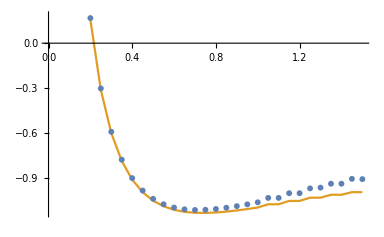

```mathematica
ListPlot[{summary[[All,{1,3}]],summary[[All,{1,4}]]},Joined->{False, True}]
```